```mathematica
mNa=;
mCs=;
```

```mathematica
ans=(Exp[-(m ω x^2)/(2ℏ)])/.{m->mNa+mCs,ℏ->Quantity["ReducedPlanckConstant"],ω->Quantity[2π 29/10,"Kilohertz"]}/.x->Quantity[x1,"Micrometers"]
```

ⅇ^(-22.3642125 x1^2)

```mathematica
√100
```

10

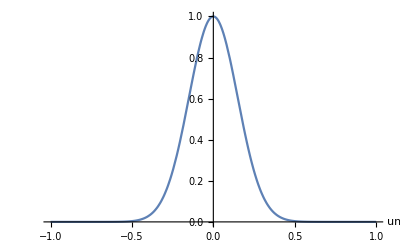

```mathematica
Plot[ans,{x1,-1,1},PlotRange->All,AxesLabel->{"um",""}]
```

```mathematica
UnitConvert[
Association[{n->0,m->mNa+mCs,ℏ->Quantity["ReducedPlanckConstant"],ω->Quantity[29,"Kilohertz"],x->Quantity[x1,"Nanometers"]}]]
```

<|n→(ⅇ^(-(m x^2 ω)/(2 ℏ)) ((m ω)/ℏ)^(1/4))/π^(1/4),m→(ⅇ^(-(m x^2 ω)/(2 ℏ)) ((m ω)/ℏ)^(1/4) HermiteH[0 u,x √((m ω)/ℏ)])/(π^(1/4) √(2^(0 u) (0 u)!)),ℏ→(ⅇ^(-(m x^2 ω)/(2 ℏ)) ((m ω)/ℏ)^(1/4) HermiteH[0 ℏ,x √((m ω)/ℏ)])/(π^(1/4) √(2^(0 ℏ) (0 ℏ)!)),ω→(ⅇ^(-(m x^2 ω)/(2 ℏ)) ((m ω)/ℏ)^(1/4) HermiteH[0 kHz,x √((m ω)/ℏ)])/(π^(1/4) √(2^(0 kHz) (0 kHz)!)),x→(ⅇ^(-(m x^2 ω)/(2 ℏ)) ((m ω)/ℏ)^(1/4) HermiteH[0 nm,x √((m ω)/ℏ)])/(π^(1/4) √(2^(0 nm) (0 nm)!))|>

22.98976928 u

```mathematica
Quantity["atomic mass of sodium"]
```

Quantity::unkunit: Unable to interpret unit specification atomic mass of sodium.

Quantity[atomic mass of sodium]

```mathematica
?HermiteH
```